Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

Problems 1 - 5. Period, “Fundamental Period”
The fundamental period is the smallest positive period.
Find it for:

1.cos x, sin x, cos 2x, sin 2x, cos πx, sin πx, cos 2πx, sin 2πx

```mathematica
Clear["Global`*"]
```

```mathematica
FunctionPeriod[{Cos[x],Sin[x]},{x,x}]
```

{2 π,2 π}

```mathematica
FunctionPeriod[{Cos[2 x],Sin[2 x]},{x,x}]
```

{π,π}

```mathematica
FunctionPeriod[{Cos[Pi x],Sin[Pi x]},{x,x}]
```

{2,2}

```mathematica
FunctionPeriod[{Cos[2Pi x],Sin[2 Pi x]},{x,x}]
```

{1,1}

There is some disagreement about what a fundamental period is. The text would have the last two results as {1,1} and {1/2, 1/2} (though it agrees with the first two).

```mathematica
Clear["Global`*"]
```

```mathematica
tre = Cos[2 Pi x]
```

```mathematica
Cos[2 π x]
tre2 = Cos[x]
```

Cos[2 π x]

Cos[x]

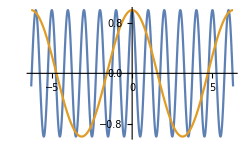

```mathematica
Plot[{tre,tre2}, {x,-2Pi,2Pi}]
```

It seems inconsistent to me to hold that the fundamental period of tre is 1/2 while that of tre2 is 2 Pi. I think the MM A convention for the period of the former is to be preferred, and it seems to agree with the initial explanation and initial plot in the text.

-----------------------------------------------------------------
Problems 6 - 10. Graphs of 2 π - periodic functions.
Sketch or graph f (x) which for - π < x < π is given as follows.

7. f(x) = |sin x|, f(x) = sin|x|

```mathematica
Clear["Global`*"]
```

```mathematica
absw=Abs[Sin[x]]
```

Abs[Sin[x]]

```mathematica
absp=Sin[Abs[x]]
```

Sin[Abs[x]]

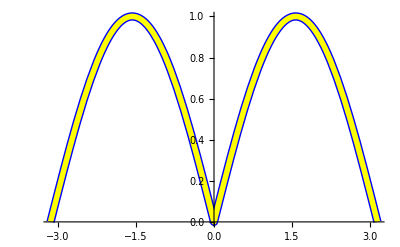

```mathematica
(*plot1 = Plot[absw, {x,-Pi,Pi}, PlotStyle->{Yellow, Thickness[0.005]},ImageSize->250];*)
plot1 = Plot[absw, {x,-Pi,Pi}, PlotStyle->{Yellow, Thickness[0.01]}];
plot2= Plot[absp,{x, -Pi, Pi}, PlotStyle->{Blue,Thickness[0.015]}];
Show[plot2, plot1]
```

Golden Arches!

9. f(x) = Piecewise[{{x, if -π < x < 0}, {π-x, if 0<x<π}}]

```mathematica
Clear["Global`*"]
```

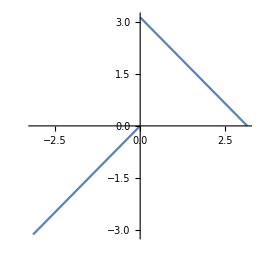

```mathematica
Plot[Piecewise[{{x, -Pi<x<0},{Pi-x,0<x<Pi}}],{x,-Pi,Pi},AspectRatio->Automatic]
```

Problems 12 - 31. Fourier Series. Find the Fourier series of the given function f (x), which is assumed to have the period 2π. Sketch or graph the partial sums up to that including cos 5x and sin 5x.

13. f(x) in problem 9.

```mathematica
e1 =ExpToTrig[FourierSeries[Piecewise[{{x, -Pi<x<0},{Pi-x,0<x<Pi}}],x,6]]
```

(4 Cos[x])/π+(4 Cos[3 x])/(9 π)+(4 Cos[5 x])/(25 π)+2 Sin[x]+2/3 Sin[3 x]+2/5 Sin[5 x]

This answer agrees with text’s, except it doesn’t show the ellipsis at the end of each half of the series expression.

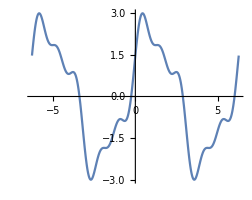

```mathematica
Plot[e1, {x, -2π,2π}, AspectRatio->Automatic]
```

15. f(x) =x^2  (0 < x < 2π)

```mathematica
e2=ExpToTrig[FourierSeries[x^2, x, 4]]
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]

The above answer does not agree with the text. Some surfing to a couple of sites shows that the answer is correct; however, the text has in mind a hand process to illustrate the basic theoretical procedure. Thus, in this problem, the text retains the sine half of the answer, even though, as an even function, the Fourier series for the problem function drops all sine parts.

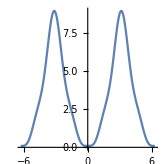

```mathematica
Plot[e2, {x, -2π,2π}, AspectRatio->Automatic]
```

17. f(x) =Piecewise[{{π+x, if -π <x <0}, {π-x, if 0<x<π}}]

```mathematica
e3 =ExpToTrig[FourierSeries[Piecewise[{{π+x, -Pi<x<0},{Pi-x,0<x<Pi}}],x,6]]
```

π/2+(4 Cos[x])/π+(4 Cos[3 x])/(9 π)+(4 Cos[5 x])/(25 π)

```mathematica
e4=Piecewise[{{π+x, -Pi<x<0},{Pi-x,0<x<Pi}}, {x,-π,π}]
```

Piecewise[{{π+x, -π<x<0}, {π-x, 0<x<π}, {{x,-π,π}, True}}]

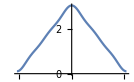
-Graphics- -Graphics-

```mathematica
p1 =Plot[e3, {x, -π, π}]; p2 =Plot[e4, {x, -π,π}];
Show[p1] Show[p2]
```

The answer, e3, agrees with the text answer. The problem was posed graphically as e4, and it is interesting to see the conformance obtained by the specified number of terms.

19. f(x) =Piecewise[{{0, if -π <x <0}, {x, if 0<x<π}}]

```mathematica
Clear["Global`*"]
```

```mathematica
e1 =ExpToTrig[FourierSeries[Piecewise[{{0, -Pi<x<0},{x,0<x<Pi}}],x,6]]
```

```mathematica
π/4-(2 Cos[x])/π-(2 Cos[3 x])/(9 π)-(2 Cos[5 x])/(25 π)+Sin[x]-1/2 Sin[2 x]+1/3 Sin[3 x]-1/4 Sin[4 x]+1/5 Sin[5 x]-1/6 Sin[6 x]
```

```mathematica
e2=Piecewise[{{0, -Pi<x<0},{x,0<x<Pi}}, {x,-π,π}]
```

Piecewise[{{0, -π<x<0}, {x, 0<x<π}, {{x,-π,π}, True}}]

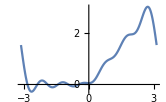
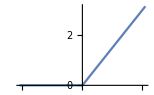

```mathematica
p1 =Plot[e1, {x, -π, π}]; p2 =Plot[e2, {x, -π,π}];
Show[p1] Show[p2]
```

The answer, e1, agrees with the text answer. The problem was posed graphically as e2, and it is interesting to see the conformance obtained by the specified number of terms.

21. f(x) =Piecewise[{{-x-π, if -π <x <0}, {-x+π, if 0<x<π}}]

```mathematica
Clear["Global`*"]
```

```mathematica
e1 =ExpToTrig[FourierSeries[Piecewise[{{-x-π, -Pi<x<0},{-x+π,0<x<Pi}}],x,6]]
```

2 Sin[x]+Sin[2 x]+2/3 Sin[3 x]+1/2 Sin[4 x]+2/5 Sin[5 x]+1/3 Sin[6 x]

```mathematica
e2=Piecewise[{{-x-π, -Pi<x<0},{-x+π,0<x<Pi}}, {x,-π,π}]
```

Piecewise[{{-π-x, -π<x<0}, {π-x, 0<x<π}, {{x,-π,π}, True}}]

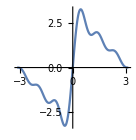
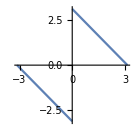

```mathematica
p1 =Plot[e1, {x, -π, π},AspectRatio->Automatic]; p2 =Plot[e2, {x, -π,π},AspectRatio->Automatic];
Show[p1] Show[p2]
```

The answer, e1, agrees with the text answer. The problem was posed graphically as e2.